```mathematica
Rho1s=300;
C1s=1377;
k1s=0.082;
Rho2s=862;
C2s=2100;
k2s=0.37;
Rho3s=74.2;
C3s=1726;
k3s=0.045;
Rho4s=1.18;
C4s=1005;
k4s=0.028;
ks=11;
a1s=k1s/(C1s*Rho1s);
a2s=k2s/(C2s*Rho2s);
a3s=k3s/(C3s*Rho3s);
a4s=k4s/(C4s*Rho4s);
x1s=0.0006;x2s=0.006;x3s=0.0036;x4s=0.005;ts=1700;
```

```mathematica
Sol=Table[0,{i,1,109},{j,1,170001}];
For[cnt=1,cnt≤170001,cnt++,Sol[[1]][[cnt]]=75;Sol[[109]][[cnt]]=37
]
For[cnt=2,cnt≤109,cnt++,Sol[[cnt]][[1]]=37
]
```

```mathematica
dy=0.01;dx1=0.0001;dx2=0.0001;dx3=0.0001;dx4=0.001;
sigma1=a1s*dy/(dx1*dx1);sigma2=a2s*dy/(dx2*dx2);sigma3=a3s*dy/(dx3*dx3);sigma4=a4s*dy/(dx4*dx4);
```

```mathematica
For[j=2,j≤170001,j++,
{
For[i=2,i≤6,i++,
Sol[[i]][[j]]=sigma1*Sol[[i+1]][[j-1]]+sigma1*Sol[[i-1]][[j-1]]-(2*sigma1-1)*Sol[[i]][[j-1]]
];
For[i=8,i≤66,i++,
Sol[[i]][[j]]=sigma2*Sol[[i+1]][[j-1]]+sigma2*Sol[[i-1]][[j-1]]-(2*sigma2-1)*Sol[[i]][[j-1]]
];
For[i=68,i≤102,i++,
Sol[[i]][[j]]=sigma3*Sol[[i+1]][[j-1]]+sigma3*Sol[[i-1]][[j-1]]-(2*sigma3-1)*Sol[[i]][[j-1]]
];
For[i=104,i≤107,i++,
Sol[[i]][[j]]=sigma4*Sol[[i+1]][[j-1]]+sigma4*Sol[[i-1]][[j-1]]-(2*sigma4-1)*Sol[[i]][[j-1]]
];
Sol[[7]][[j]]=(Sol[[8]][[j]]-Sol[[6]][[j]])/(k1s/dx1+k2s/dx2)*k2s/dx2+Sol[[6]][[j]];
Sol[[67]][[j]]=(Sol[[68]][[j]]-Sol[[66]][[j]])/(k2s/dx2+k3s/dx3)*k3s/dx3+Sol[[66]][[j]];
Sol[[103]][[j]]=(Sol[[104]][[j]]-Sol[[102]][[j]])/(k3s/dx3+ks)*ks+Sol[[102]][[j]];
Sol[[108]][[j]]=(Sol[[109]][[j]]-Sol[[107]][[j]])/(k4s/dx4+ks)*ks+Sol[[107]][[j]]
}
]
```

```mathematica
mesh=Table[Sol[[i]][[100*j+1]],{i,1,109},{j,0,1700}];
```

```mathematica
data=Import["D:\\Mod\\temperature.xlsx"];
```

```mathematica
actual=Table[data[[1]][[i]][[2]],{i,3,1703}];
```

```mathematica
mesh[[108]]
```

{37,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.0001,37.0002,37.0005,37.001,37.0018,37.0031,37.0051,37.0079,37.0115,37.0163,37.0223,37.0296,37.0384,37.0487,37.0606,37.0742,37.0895,37.1066,37.1255,37.1461,37.1686,37.1927,37.2187,37.2463,37.2756,37.3065,37.3391,37.3731,37.4086,37.4456,37.4839,37.5235,37.5643,37.6064,37.6495,37.6938,37.739,37.7852,37.8323,37.8802,37.9289,37.9783,38.0284,38.0792,38.1305,38.1823,38.2347,38.2875,38.3407,38.3942,38.4481,38.5023,38.5567,38.6114,38.6663,38.7213,38.7764,38.8317,38.8871,38.9425,38.9979,39.0534,39.1088,39.1643,39.2196,39.275,39.3302,39.3853,39.4404,39.4953,39.5501,39.6047,39.6592,39.7135,39.7676,39.8216,39.8753,39.9288,39.9821,40.0352,40.0881,40.1408,40.1932,40.2453,40.2972,40.3489,40.4003,40.4515,40.5024,40.553,40.6033,40.6534,40.7032,40.7527,40.802,40.851,40.8997,40.9481,40.9962,41.0441,41.0916,41.1389,41.1859,41.2326,41.279,41.3252,41.371,41.4166,41.4619,41.5069,41.5516,41.5961,41.6402,41.6841,41.7277,41.771,41.8141,41.8568,41.8993,41.9415,41.9835,42.0251,42.0665,42.1077,42.1485,42.1891,42.2294,42.2695,42.3093,42.3488,42.388,42.427,42.4658,42.5043,42.5425,42.5805,42.6182,42.6557,42.6929,42.7298,42.7666,42.803,42.8393,42.8752,42.911,42.9465,42.9818,43.0168,43.0516,43.0861,43.1205,43.1546,43.1884,43.2221,43.2555,43.2887,43.3216,43.3543,43.3869,43.4192,43.4512,43.4831,43.5147,43.5462,43.5774,43.6084,43.6392,43.6698,43.7001,43.7303,43.7603,43.79,43.8196,43.849,43.8781,43.9071,43.9359,43.9644,43.9928,44.021,44.049,44.0768,44.1044,44.1319,44.1591,44.1862,44.213,44.2397,44.2662,44.2926,44.3187,44.3447,44.3705,44.3961,44.4215,44.4468,44.4719,44.4969,44.5216,44.5462,44.5706,44.5949,44.619,44.6429,44.6667,44.6903,44.7138,44.737,44.7602,44.7831,44.806,44.8286,44.8511,44.8735,44.8957,44.9177,44.9396,44.9614,44.983,45.0045,45.0258,45.0469,45.068,45.0888,45.1096,45.1302,45.1506,45.1709,45.1911,45.2112,45.2311,45.2508,45.2705,45.29,45.3094,45.3286,45.3477,45.3667,45.3855,45.4043,45.4228,45.4413,45.4597,45.4779,45.496,45.5139,45.5318,45.5495,45.5671,45.5846,45.602,45.6192,45.6363,45.6534,45.6703,45.687,45.7037,45.7203,45.7367,45.753,45.7693,45.7854,45.8014,45.8173,45.8331,45.8487,45.8643,45.8798,45.8951,45.9104,45.9255,45.9406,45.9555,45.9704,45.9851,45.9998,46.0143,46.0287,46.0431,46.0573,46.0715,46.0855,46.0995,46.1134,46.1271,46.1408,46.1544,46.1679,46.1813,46.1946,46.2078,46.2209,46.234,46.2469,46.2598,46.2726,46.2853,46.2979,46.3104,46.3228,46.3352,46.3474,46.3596,46.3717,46.3837,46.3956,46.4075,46.4193,46.4309,46.4426,46.4541,46.4655,46.4769,46.4882,46.4994,46.5106,46.5217,46.5326,46.5436,46.5544,46.5652,46.5759,46.5865,46.5971,46.6075,46.6179,46.6283,46.6386,46.6488,46.6589,46.6689,46.6789,46.6889,46.6987,46.7085,46.7182,46.7279,46.7375,46.747,46.7565,46.7659,46.7752,46.7845,46.7937,46.8028,46.8119,46.8209,46.8299,46.8388,46.8476,46.8564,46.8651,46.8738,46.8824,46.8909,46.8994,46.9078,46.9162,46.9245,46.9327,46.9409,46.9491,46.9572,46.9652,46.9732,46.9811,46.989,46.9968,47.0045,47.0123,47.0199,47.0275,47.0351,47.0426,47.05,47.0574,47.0648,47.0721,47.0793,47.0865,47.0937,47.1008,47.1078,47.1148,47.1218,47.1287,47.1356,47.1424,47.1492,47.1559,47.1626,47.1692,47.1758,47.1823,47.1889,47.1953,47.2017,47.2081,47.2144,47.2207,47.2269,47.2331,47.2393,47.2454,47.2515,47.2575,47.2635,47.2694,47.2753,47.2812,47.287,47.2928,47.2986,47.3043,47.31,47.3156,47.3212,47.3267,47.3323,47.3377,47.3432,47.3486,47.354,47.3593,47.3646,47.3699,47.3751,47.3803,47.3854,47.3905,47.3956,47.4007,47.4057,47.4107,47.4156,47.4205,47.4254,47.4303,47.4351,47.4399,47.4446,47.4493,47.454,47.4587,47.4633,47.4679,47.4724,47.477,47.4815,47.4859,47.4904,47.4948,47.4991,47.5035,47.5078,47.5121,47.5163,47.5206,47.5248,47.5289,47.5331,47.5372,47.5413,47.5454,47.5494,47.5534,47.5574,47.5613,47.5652,47.5691,47.573,47.5768,47.5807,47.5845,47.5882,47.592,47.5957,47.5994,47.603,47.6067,47.6103,47.6139,47.6174,47.621,47.6245,47.628,47.6315,47.6349,47.6383,47.6417,47.6451,47.6485,47.6518,47.6551,47.6584,47.6616,47.6649,47.6681,47.6713,47.6745,47.6776,47.6808,47.6839,47.687,47.69,47.6931,47.6961,47.6991,47.7021,47.7051,47.708,47.7109,47.7138,47.7167,47.7196,47.7224,47.7253,47.7281,47.7309,47.7336,47.7364,47.7391,47.7418,47.7445,47.7472,47.7499,47.7525,47.7551,47.7577,47.7603,47.7629,47.7654,47.768,47.7705,47.773,47.7755,47.7779,47.7804,47.7828,47.7852,47.7876,47.79,47.7924,47.7947,47.7971,47.7994,47.8017,47.804,47.8063,47.8085,47.8108,47.813,47.8152,47.8174,47.8196,47.8217,47.8239,47.826,47.8282,47.8303,47.8324,47.8344,47.8365,47.8386,47.8406,47.8426,47.8446,47.8466,47.8486,47.8506,47.8525,47.8545,47.8564,47.8583,47.8602,47.8621,47.864,47.8659,47.8677,47.8695,47.8714,47.8732,47.875,47.8768,47.8786,47.8803,47.8821,47.8838,47.8855,47.8873,47.889,47.8907,47.8923,47.894,47.8957,47.8973,47.899,47.9006,47.9022,47.9038,47.9054,47.907,47.9086,47.9101,47.9117,47.9132,47.9147,47.9163,47.9178,47.9193,47.9208,47.9222,47.9237,47.9252,47.9266,47.9281,47.9295,47.9309,47.9323,47.9337,47.9351,47.9365,47.9379,47.9392,47.9406,47.9419,47.9432,47.9446,47.9459,47.9472,47.9485,47.9498,47.9511,47.9523,47.9536,47.9549,47.9561,47.9573,47.9586,47.9598,47.961,47.9622,47.9634,47.9646,47.9658,47.9669,47.9681,47.9693,47.9704,47.9716,47.9727,47.9738,47.9749,47.976,47.9771,47.9782,47.9793,47.9804,47.9815,47.9825,47.9836,47.9847,47.9857,47.9867,47.9878,47.9888,47.9898,47.9908,47.9918,47.9928,47.9938,47.9948,47.9958,47.9967,47.9977,47.9986,47.9996,48.0005,48.0015,48.0024,48.0033,48.0042,48.0052,48.0061,48.007,48.0078,48.0087,48.0096,48.0105,48.0114,48.0122,48.0131,48.0139,48.0148,48.0156,48.0164,48.0173,48.0181,48.0189,48.0197,48.0205,48.0213,48.0221,48.0229,48.0237,48.0245,48.0252,48.026,48.0268,48.0275,48.0283,48.029,48.0298,48.0305,48.0312,48.032,48.0327,48.0334,48.0341,48.0348,48.0355,48.0362,48.0369,48.0376,48.0383,48.039,48.0396,48.0403,48.041,48.0416,48.0423,48.043,48.0436,48.0442,48.0449,48.0455,48.0461,48.0468,48.0474,48.048,48.0486,48.0492,48.0498,48.0504,48.051,48.0516,48.0522,48.0528,48.0534,48.054,48.0545,48.0551,48.0557,48.0562,48.0568,48.0573,48.0579,48.0584,48.059,48.0595,48.06,48.0606,48.0611,48.0616,48.0621,48.0627,48.0632,48.0637,48.0642,48.0647,48.0652,48.0657,48.0662,48.0667,48.0672,48.0676,48.0681,48.0686,48.0691,48.0695,48.07,48.0705,48.0709,48.0714,48.0718,48.0723,48.0727,48.0732,48.0736,48.0741,48.0745,48.0749,48.0754,48.0758,48.0762,48.0766,48.0771,48.0775,48.0779,48.0783,48.0787,48.0791,48.0795,48.0799,48.0803,48.0807,48.0811,48.0815,48.0819,48.0822,48.0826,48.083,48.0834,48.0838,48.0841,48.0845,48.0849,48.0852,48.0856,48.0859,48.0863,48.0866,48.087,48.0873,48.0877,48.088,48.0884,48.0887,48.089,48.0894,48.0897,48.09,48.0904,48.0907,48.091,48.0913,48.0917,48.092,48.0923,48.0926,48.0929,48.0932,48.0935,48.0938,48.0941,48.0944,48.0947,48.095,48.0953,48.0956,48.0959,48.0962,48.0965,48.0967,48.097,48.0973,48.0976,48.0979,48.0981,48.0984,48.0987,48.0989,48.0992,48.0995,48.0997,48.1,48.1003,48.1005,48.1008,48.101,48.1013,48.1015,48.1018,48.102,48.1023,48.1025,48.1028,48.103,48.1032,48.1035,48.1037,48.1039,48.1042,48.1044,48.1046,48.1049,48.1051,48.1053,48.1055,48.1058,48.106,48.1062,48.1064,48.1066,48.1069,48.1071,48.1073,48.1075,48.1077,48.1079,48.1081,48.1083,48.1085,48.1087,48.1089,48.1091,48.1093,48.1095,48.1097,48.1099,48.1101,48.1103,48.1105,48.1107,48.1108,48.111,48.1112,48.1114,48.1116,48.1118,48.1119,48.1121,48.1123,48.1125,48.1126,48.1128,48.113,48.1132,48.1133,48.1135,48.1137,48.1138,48.114,48.1142,48.1143,48.1145,48.1147,48.1148,48.115,48.1151,48.1153,48.1154,48.1156,48.1157,48.1159,48.1161,48.1162,48.1164,48.1165,48.1166,48.1168,48.1169,48.1171,48.1172,48.1174,48.1175,48.1176,48.1178,48.1179,48.1181,48.1182,48.1183,48.1185,48.1186,48.1187,48.1189,48.119,48.1191,48.1193,48.1194,48.1195,48.1196,48.1198,48.1199,48.12,48.1201,48.1203,48.1204,48.1205,48.1206,48.1207,48.1209,48.121,48.1211,48.1212,48.1213,48.1214,48.1216,48.1217,48.1218,48.1219,48.122,48.1221,48.1222,48.1223,48.1224,48.1225,48.1227,48.1228,48.1229,48.123,48.1231,48.1232,48.1233,48.1234,48.1235,48.1236,48.1237,48.1238,48.1239,48.124,48.1241,48.1242,48.1243,48.1244,48.1244,48.1245,48.1246,48.1247,48.1248,48.1249,48.125,48.1251,48.1252,48.1253,48.1253,48.1254,48.1255,48.1256,48.1257,48.1258,48.1259,48.1259,48.126,48.1261,48.1262,48.1263,48.1264,48.1264,48.1265,48.1266,48.1267,48.1268,48.1268,48.1269,48.127,48.1271,48.1271,48.1272,48.1273,48.1274,48.1274,48.1275,48.1276,48.1276,48.1277,48.1278,48.1279,48.1279,48.128,48.1281,48.1281,48.1282,48.1283,48.1283,48.1284,48.1285,48.1285,48.1286,48.1287,48.1287,48.1288,48.1289,48.1289,48.129,48.129,48.1291,48.1292,48.1292,48.1293,48.1294,48.1294,48.1295,48.1295,48.1296,48.1296,48.1297,48.1298,48.1298,48.1299,48.1299,48.13,48.13,48.1301,48.1302,48.1302,48.1303,48.1303,48.1304,48.1304,48.1305,48.1305,48.1306,48.1306,48.1307,48.1307,48.1308,48.1308,48.1309,48.1309,48.131,48.131,48.1311,48.1311,48.1312,48.1312,48.1313,48.1313,48.1314,48.1314,48.1315,48.1315,48.1315,48.1316,48.1316,48.1317,48.1317,48.1318,48.1318,48.1319,48.1319,48.1319,48.132,48.132,48.1321,48.1321,48.1321,48.1322,48.1322,48.1323,48.1323,48.1323,48.1324,48.1324,48.1325,48.1325,48.1325,48.1326,48.1326,48.1327,48.1327,48.1327,48.1328,48.1328,48.1328,48.1329,48.1329,48.1329,48.133,48.133,48.1331,48.1331,48.1331,48.1332,48.1332,48.1332,48.1333,48.1333,48.1333,48.1334,48.1334,48.1334,48.1335,48.1335,48.1335,48.1336,48.1336,48.1336,48.1336,48.1337,48.1337,48.1337,48.1338,48.1338,48.1338,48.1339,48.1339,48.1339,48.1339,48.134,48.134,48.134,48.1341,48.1341,48.1341,48.1341,48.1342,48.1342,48.1342,48.1342,48.1343,48.1343,48.1343,48.1344,48.1344,48.1344,48.1344,48.1345,48.1345,48.1345,48.1345,48.1346,48.1346,48.1346,48.1346,48.1346,48.1347,48.1347,48.1347,48.1347,48.1348,48.1348,48.1348,48.1348,48.1349,48.1349,48.1349,48.1349,48.1349,48.135,48.135,48.135,48.135,48.1351,48.1351,48.1351,48.1351,48.1351,48.1352,48.1352,48.1352,48.1352,48.1352,48.1353,48.1353,48.1353,48.1353,48.1353,48.1354,48.1354,48.1354,48.1354,48.1354,48.1354,48.1355,48.1355,48.1355,48.1355,48.1355,48.1356,48.1356,48.1356,48.1356,48.1356,48.1356,48.1357,48.1357,48.1357,48.1357,48.1357,48.1357,48.1358,48.1358,48.1358,48.1358,48.1358,48.1358,48.1359,48.1359,48.1359,48.1359,48.1359,48.1359,48.1359,48.136,48.136,48.136,48.136,48.136,48.136,48.1361,48.1361,48.1361,48.1361,48.1361,48.1361,48.1361,48.1362,48.1362,48.1362,48.1362,48.1362,48.1362,48.1362,48.1362,48.1363,48.1363,48.1363,48.1363,48.1363,48.1363,48.1363,48.1363,48.1364,48.1364,48.1364,48.1364,48.1364,48.1364,48.1364,48.1364,48.1365,48.1365,48.1365,48.1365,48.1365,48.1365,48.1365,48.1365,48.1365,48.1366,48.1366,48.1366,48.1366,48.1366,48.1366,48.1366,48.1366,48.1366,48.1366,48.1367,48.1367,48.1367,48.1367,48.1367,48.1367,48.1367,48.1367,48.1367,48.1367,48.1368,48.1368,48.1368,48.1368,48.1368,48.1368,48.1368,48.1368,48.1368,48.1368,48.1368,48.1369,48.1369,48.1369,48.1369,48.1369,48.1369,48.1369,48.1369,48.1369,48.1369,48.1369,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.137,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1371,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1372,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1373,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1374,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1375,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1376,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1377,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1378,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.1379,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138,48.138}

```mathematica
actual-mesh[[108]]
```

{0.,0.,0.,0.,-2.29505×10^-12,-7.39064×10^-10,-3.37786×10^-8,-5.12684×10^-7,-3.92931×10^-6,-0.0000191505,-0.0000680889,-0.000192629,-0.000459333,-0.000960564,-0.0018121,-0.00314815,0.00488491,0.00213519,-0.00154872,-0.00631251,-0.00229214,-0.00961093,-0.0083776,-0.0186852,-0.0206109,-0.024216,-0.0295465,-0.0366341,-0.0454971,-0.0561419,-0.0685635,-0.0727475,-0.0886706,-0.0963022,-0.115605,-0.126537,-0.139051,-0.153095,-0.168617,-0.18556,-0.203867,-0.213477,-0.234333,-0.246374,-0.26954,-0.283771,-0.29901,-0.325197,-0.342277,-0.360194,-0.378893,-0.398321,-0.418428,-0.429164,-0.450481,-0.472333,-0.494674,-0.507463,-0.530658,-0.54422,-0.56811,-0.592293,-0.606735,-0.621402,-0.646262,-0.661287,-0.686447,-0.701716,-0.717068,-0.742479,-0.757925,-0.773384,-0.788837,-0.814263,-0.829644,-0.844963,-0.860203,-0.885349,-0.900386,-0.915301,-0.93008,-0.954712,-0.969185,-0.983489,-0.997614,-1.01155,-1.03529,-1.04882,-1.06214,-1.07525,-1.09812,-1.11076,-1.12317,-1.13533,-1.15725,-1.16891,-1.18032,-1.19147,-1.21235,-1.22297,-1.23332,-1.2534,-1.2632,-1.27273,-1.28199,-1.30096,-1.30966,-1.32807,-1.3362,-1.34405,-1.36162,-1.3689,-1.38589,-1.39261,-1.40903,-1.41518,-1.42104,-1.43661,-1.4419,-1.45691,-1.46164,-1.47608,-1.49024,-1.49412,-1.50772,-1.51104,-1.52408,-1.53684,-1.53933,-1.55154,-1.55348,-1.56515,-1.57654,-1.58766,-1.58851,-1.5991,-1.60941,-1.60946,-1.61925,-1.62877,-1.63804,-1.64704,-1.64578,-1.65426,-1.66249,-1.67046,-1.67818,-1.68565,-1.69287,-1.69984,-1.69656,-1.70303,-1.70926,-1.71525,-1.72099,-1.7265,-1.73176,-1.73679,-1.74159,-1.74614,-1.75047,-1.75456,-1.76843,-1.77206,-1.77547,-1.77865,-1.78161,-1.78435,-1.78686,-1.78915,-1.80123,-1.80309,-1.80473,-1.80616,-1.80738,-1.81838,-1.81918,-1.81976,-1.82014,-1.83031,-1.83028,-1.83004,-1.83961,-1.83897,-1.83813,-1.8471,-1.84587,-1.84444,-1.85282,-1.85101,-1.859,-1.85681,-1.85442,-1.86185,-1.85909,-1.86615,-1.86303,-1.86972,-1.86623,-1.87256,-1.86871,-1.87468,-1.87048,-1.8761,-1.88155,-1.87682,-1.88192,-1.87686,-1.88162,-1.87621,-1.88064,-1.8849,-1.879,-1.88293,-1.8867,-1.88031,-1.88376,-1.88704,-1.89017,-1.88315,-1.88596,-1.88863,-1.88113,-1.88349,-1.88569,-1.88774,-1.88964,-1.8814,-1.883,-1.88446,-1.88577,-1.88694,-1.87796,-1.87884,-1.87958,-1.88017,-1.88063,-1.88095,-1.88113,-1.88117,-1.88108,-1.88085,-1.87048,-1.86999,-1.86936,-1.8686,-1.8677,-1.86668,-1.86553,-1.86425,-1.86284,-1.86131,-1.85965,-1.85787,-1.85596,-1.85393,-1.86178,-1.8595,-1.85711,-1.85459,-1.85196,-1.84921,-1.84634,-1.84336,-1.84026,-1.83704,-1.84371,-1.84027,-1.83671,-1.83304,-1.82926,-1.82537,-1.83138,-1.82727,-1.82305,-1.81873,-1.8143,-1.81976,-1.81512,-1.81038,-1.80553,-1.81058,-1.80552,-1.80037,-1.80511,-1.79975,-1.7943,-1.78874,-1.79309,-1.78734,-1.78149,-1.78554,-1.7795,-1.77337,-1.77714,-1.77082,-1.7744,-1.76789,-1.76129,-1.7646,-1.75782,-1.76095,-1.75398,-1.74693,-1.7498,-1.74257,-1.74526,-1.73786,-1.74038,-1.73281,-1.72515,-1.72742,-1.71959,-1.72169,-1.7137,-1.71564,-1.70749,-1.70926,-1.70095,-1.70256,-1.70409,-1.69554,-1.69692,-1.68822,-1.68944,-1.68058,-1.68165,-1.67265,-1.67357,-1.67441,-1.66518,-1.66588,-1.6565,-1.65706,-1.65754,-1.64795,-1.64829,-1.64856,-1.63875,-1.63888,-1.63894,-1.62894,-1.62886,-1.62872,-1.61851,-1.61823,-1.61789,-1.60748,-1.607,-1.60646,-1.59586,-1.59519,-1.59446,-1.59367,-1.58281,-1.5819,-1.58092,-1.57987,-1.56877,-1.56761,-1.56639,-1.5651,-1.56376,-1.55236,-1.5509,-1.54938,-1.54781,-1.53618,-1.53449,-1.53274,-1.53094,-1.52908,-1.52717,-1.5152,-1.51318,-1.5111,-1.50897,-1.50679,-1.50455,-1.50226,-1.48991,-1.48752,-1.48507,-1.48258,-1.48003,-1.47743,-1.47478,-1.47208,-1.46933,-1.46653,-1.45368,-1.45078,-1.44784,-1.44485,-1.44181,-1.43872,-1.43558,-1.4324,-1.42917,-1.4259,-1.42258,-1.41922,-1.4158,-1.41235,-1.40885,-1.40531,-1.40172,-1.39809,-1.39441,-1.3907,-1.38693,-1.38313,-1.37929,-1.3754,-1.37147,-1.3675,-1.36349,-1.35944,-1.35535,-1.35122,-1.34704,-1.34283,-1.33858,-1.33429,-1.33996,-1.3356,-1.33119,-1.32675,-1.32226,-1.31774,-1.31319,-1.30859,-1.30396,-1.2993,-1.29459,-1.29986,-1.29508,-1.29027,-1.28543,-1.28054,-1.27563,-1.27068,-1.27569,-1.27068,-1.26562,-1.26054,-1.25542,-1.25027,-1.24508,-1.24986,-1.24461,-1.23933,-1.23401,-1.22866,-1.23329,-1.22788,-1.22243,-1.21696,-1.21146,-1.21592,-1.21036,-1.20477,-1.19914,-1.19349,-1.1978,-1.19209,-1.18635,-1.18058,-1.17478,-1.17895,-1.17309,-1.16721,-1.16129,-1.16535,-1.15939,-1.15339,-1.14737,-1.15132,-1.14524,-1.13914,-1.14301,-1.13685,-1.13067,-1.12446,-1.12822,-1.12196,-1.11568,-1.11937,-1.11303,-1.10667,-1.10029,-1.10388,-1.09744,-1.09098,-1.0945,-1.08799,-1.08146,-1.08491,-1.07833,-1.07173,-1.07511,-1.06846,-1.06179,-1.0651,-1.05838,-1.05165,-1.05489,-1.04811,-1.0413,-1.04448,-1.03763,-1.04076,-1.03387,-1.02696,-1.03003,-1.02308,-1.01611,-1.01911,-1.0121,-1.01506,-1.00801,-1.00094,-1.00384,-0.996727,-0.999593,-0.99244,-0.985267,-0.988075,-0.980864,-0.983634,-0.976385,-0.969117,-0.971831,-0.964527,-0.967204,-0.959863,-0.962503,-0.955126,-0.947731,-0.950318,-0.942888,-0.94544,-0.937975,-0.940493,-0.932993,-0.935476,-0.927943,-0.930393,-0.922826,-0.915242,-0.917643,-0.910026,-0.912394,-0.904745,-0.907081,-0.899401,-0.901704,-0.893993,-0.896265,-0.888522,-0.890764,-0.882991,-0.885202,-0.877399,-0.87958,-0.871747,-0.873899,-0.866036,-0.868158,-0.860267,-0.862361,-0.85444,-0.856506,-0.848557,-0.850595,-0.842619,-0.844629,-0.836625,-0.838607,-0.830577,-0.832532,-0.824475,-0.826404,-0.82832,-0.820224,-0.822114,-0.813991,-0.815856,-0.807707,-0.809547,-0.801374,-0.803188,-0.79499,-0.79678,-0.798557,-0.790323,-0.792076,-0.783818,-0.785548,-0.777266,-0.778972,-0.780666,-0.77235,-0.774021,-0.765682,-0.767331,-0.758969,-0.760595,-0.762211,-0.753815,-0.755409,-0.746992,-0.748564,-0.750126,-0.741676,-0.743217,-0.734746,-0.736266,-0.737775,-0.729274,-0.730762,-0.722241,-0.723709,-0.725168,-0.716616,-0.718055,-0.709484,-0.710903,-0.712312,-0.703712,-0.705103,-0.706483,-0.697855,-0.699217,-0.69057,-0.691914,-0.693249,-0.684574,-0.685891,-0.687198,-0.678497,-0.679787,-0.681068,-0.67234,-0.673604,-0.674859,-0.666105,-0.667344,-0.658573,-0.659795,-0.661008,-0.652212,-0.653409,-0.654597,-0.645778,-0.64695,-0.648114,-0.639271,-0.640419,-0.64156,-0.632693,-0.633818,-0.634936,-0.626046,-0.627148,-0.628243,-0.619331,-0.620411,-0.621484,-0.622549,-0.613608,-0.614659,-0.615703,-0.606739,-0.607769,-0.608792,-0.599808,-0.600817,-0.601819,-0.592814,-0.593802,-0.594784,-0.595759,-0.586727,-0.587689,-0.588644,-0.579593,-0.580536,-0.581472,-0.572401,-0.573324,-0.574241,-0.575152,-0.566057,-0.566955,-0.567847,-0.558733,-0.559614,-0.560488,-0.561356,-0.552218,-0.553075,-0.553925,-0.55477,-0.545609,-0.546443,-0.547271,-0.538093,-0.538909,-0.53972,-0.540526,-0.531326,-0.53212,-0.532909,-0.533693,-0.524471,-0.525245,-0.526012,-0.526775,-0.517533,-0.518285,-0.519032,-0.519774,-0.510511,-0.511243,-0.51197,-0.512692,-0.50341,-0.504122,-0.50483,-0.505532,-0.49623,-0.496923,-0.497612,-0.498296,-0.488975,-0.489649,-0.490319,-0.490984,-0.481645,-0.482302,-0.482953,-0.483601,-0.484244,-0.474883,-0.475517,-0.476147,-0.476773,-0.467394,-0.468011,-0.468624,-0.469233,-0.469838,-0.460439,-0.461035,-0.461628,-0.462216,-0.4528,-0.453381,-0.453957,-0.45453,-0.455099,-0.445664,-0.446225,-0.446782,-0.447335,-0.447885,-0.438431,-0.438973,-0.439511,-0.440046,-0.440577,-0.431105,-0.431629,-0.432149,-0.432666,-0.43318,-0.42369,-0.424196,-0.424699,-0.425198,-0.425695,-0.416187,-0.416677,-0.417163,-0.417646,-0.418125,-0.408601,-0.409074,-0.409544,-0.410011,-0.410474,-0.400935,-0.401392,-0.401846,-0.402297,-0.402745,-0.403189,-0.393631,-0.39407,-0.394506,-0.394939,-0.395369,-0.395795,-0.38622,-0.386641,-0.387059,-0.387475,-0.387887,-0.378297,-0.378704,-0.379108,-0.37951,-0.379909,-0.380305,-0.370698,-0.371089,-0.371477,-0.371863,-0.372245,-0.372626,-0.363003,-0.363378,-0.363751,-0.364121,-0.364488,-0.364853,-0.365216,-0.355576,-0.355933,-0.356288,-0.356641,-0.356991,-0.357339,-0.347685,-0.348028,-0.348369,-0.348708,-0.349044,-0.349378,-0.34971,-0.340039,-0.340366,-0.340691,-0.341014,-0.341335,-0.341653,-0.331969,-0.332283,-0.332595,-0.332905,-0.333213,-0.333518,-0.333822,-0.324123,-0.324423,-0.32472,-0.325016,-0.325309,-0.3256,-0.32589,-0.326177,-0.316463,-0.316746,-0.317028,-0.317307,-0.317585,-0.317861,-0.318135,-0.308407,-0.308677,-0.308946,-0.309213,-0.309477,-0.30974,-0.310002,-0.310261,-0.300519,-0.300775,-0.301029,-0.301281,-0.301532,-0.301781,-0.302029,-0.302274,-0.292518,-0.292761,-0.293001,-0.29324,-0.293478,-0.293714,-0.293948,-0.29418,-0.284411,-0.284641,-0.284869,-0.285095,-0.28532,-0.285543,-0.285765,-0.285985,-0.286204,-0.276421,-0.276637,-0.276851,-0.277064,-0.277276,-0.277486,-0.277694,-0.277901,-0.278107,-0.268311,-0.268514,-0.268716,-0.268916,-0.269115,-0.269312,-0.269508,-0.269703,-0.269897,-0.260089,-0.26028,-0.260469,-0.260658,-0.260845,-0.26103,-0.261215,-0.261398,-0.26158,-0.261761,-0.25194,-0.252118,-0.252295,-0.252471,-0.252646,-0.252819,-0.252992,-0.253163,-0.253333,-0.253501,-0.243669,-0.243836,-0.244001,-0.244165,-0.244328,-0.24449,-0.244651,-0.244811,-0.24497,-0.245127,-0.245284,-0.23544,-0.235594,-0.235747,-0.2359,-0.236051,-0.236201,-0.236351,-0.236499,-0.236646,-0.236792,-0.236938,-0.227082,-0.227225,-0.227368,-0.227509,-0.227649,-0.227789,-0.227927,-0.228065,-0.228201,-0.228337,-0.228472,-0.218606,-0.218739,-0.218871,-0.219002,-0.219132,-0.219261,-0.21939,-0.219517,-0.219644,-0.21977,-0.219895,-0.220019,-0.220142,-0.210265,-0.210387,-0.210507,-0.210627,-0.210746,-0.210865,-0.210982,-0.211099,-0.211215,-0.21133,-0.211445,-0.211558,-0.211671,-0.201783,-0.201895,-0.202005,-0.202115,-0.202224,-0.202332,-0.20244,-0.202547,-0.202653,-0.202758,-0.202863,-0.202967,-0.20307,-0.193173,-0.193275,-0.193376,-0.193476,-0.193576,-0.193675,-0.193774,-0.193871,-0.193969,-0.194065,-0.194161,-0.194256,-0.19435,-0.194444,-0.194538,-0.18463,-0.184722,-0.184813,-0.184904,-0.184994,-0.185084,-0.185173,-0.185261,-0.185348,-0.185436,-0.185522,-0.185608,-0.185693,-0.185778,-0.185862,-0.185946,-0.176029,-0.176111,-0.176193,-0.176274,-0.176355,-0.176435,-0.176515,-0.176594,-0.176673,-0.176751,-0.176828,-0.176905,-0.176982,-0.177058,-0.177133,-0.177208,-0.177283,-0.167356,-0.16743,-0.167503,-0.167575,-0.167647,-0.167719,-0.167789,-0.16786,-0.16793,-0.167999,-0.168068,-0.168137,-0.168205,-0.168273,-0.16834,-0.168407,-0.168473,-0.168539,-0.158604,-0.158669,-0.158734,-0.158798,-0.158861,-0.158924,-0.158987,-0.159049,-0.159111,-0.159173,-0.159234,-0.159295,-0.159355,-0.159415,-0.159474,-0.159533,-0.159592,-0.15965,-0.159708,-0.159765,-0.149822,-0.149879,-0.149935,-0.149991,-0.150046,-0.150101,-0.150156,-0.150211,-0.150265,-0.150318,-0.150372,-0.150424,-0.150477,-0.150529,-0.150581,-0.150632,-0.150684,-0.150734,-0.150785,-0.150835,-0.150885,-0.150934,-0.140983,-0.141032,-0.14108,-0.141128,-0.141176,-0.141224,-0.141271,-0.141318,-0.141364,-0.14141,-0.141456,-0.141502,-0.141547,-0.141592,-0.141636,-0.141681,-0.141725,-0.141768,-0.141812,-0.141855,-0.141898,-0.14194,-0.141982,-0.142024,-0.132066,-0.132107,-0.132148,-0.132189,-0.13223,-0.13227,-0.13231,-0.13235,-0.132389,-0.132428,-0.132467,-0.132506,-0.132544,-0.132583,-0.13262,-0.132658,-0.132695,-0.132732,-0.132769,-0.132806,-0.132842,-0.132878,-0.132914,-0.13295,-0.132985,-0.13302,-0.133055,-0.12309,-0.123124,-0.123158,-0.123192,-0.123226,-0.12326,-0.123293,-0.123326,-0.123359,-0.123391,-0.123424,-0.123456,-0.123488,-0.12352,-0.123551,-0.123582,-0.123613,-0.123644,-0.123675,-0.123705,-0.123736,-0.123766,-0.123795,-0.123825,-0.123854,-0.123884,-0.123913,-0.123942,-0.12397,-0.123999,-0.114027,-0.114055,-0.114083,-0.11411,-0.114138,-0.114165,-0.114192,-0.114219,-0.114246,-0.114272,-0.114299,-0.114325,-0.114351,-0.114377,-0.114403,-0.114428,-0.114453,-0.114479,-0.114503,-0.114528,-0.114553,-0.114577,-0.114602,-0.114626,-0.11465,-0.114674,-0.114697,-0.114721,-0.114744,-0.114767,-0.11479,-0.114813,-0.114836,-0.114858,-0.114881,-0.104903,-0.104925,-0.104947,-0.104969,-0.10499,-0.105012,-0.105033,-0.105054,-0.105076,-0.105096,-0.105117,-0.105138,-0.105158,-0.105179,-0.105199,-0.105219,-0.105239,-0.105259,-0.105278,-0.105298,-0.105317,-0.105337,-0.105356,-0.105375,-0.105394,-0.105412,-0.105431,-0.105449,-0.105468,-0.105486,-0.105504,-0.105522,-0.10554,-0.105558,-0.105575,-0.105593,-0.10561,-0.105628,-0.105645,-0.105662,-0.105679,-0.105696,-0.0957123,-0.0957289,-0.0957454,-0.0957617,-0.095778,-0.0957941,-0.0958101,-0.0958261,-0.0958419,-0.0958576,-0.0958732,-0.0958886,-0.095904,-0.0959193,-0.0959345,-0.0959496,-0.0959645,-0.0959794,-0.0959942,-0.0960088,-0.0960234,-0.0960379,-0.0960522,-0.0960665,-0.0960807,-0.0960948,-0.0961087,-0.0961226,-0.0961364,-0.0961501,-0.0961637,-0.0961772,-0.0961907,-0.096204,-0.0962172,-0.0962304,-0.0962434,-0.0962564,-0.0962693,-0.0962821,-0.0962948,-0.0963074,-0.09632,-0.0963324,-0.0963448,-0.0963571,-0.0963693,-0.0963814,-0.0963934,-0.0964054,-0.0964172,-0.086429,-0.0864407,-0.0864523,-0.0864639,-0.0864754,-0.0864868,-0.0864981,-0.0865093,-0.0865205,-0.0865316,-0.0865426,-0.0865535,-0.0865644,-0.0865752,-0.0865859,-0.0865965,-0.0866071,-0.0866176,-0.086628,-0.0866384,-0.0866487,-0.0866589,-0.086669,-0.0866791,-0.0866891,-0.086699,-0.0867089,-0.0867187,-0.0867285,-0.0867381,-0.0867477,-0.0867573,-0.0867668,-0.0867762,-0.0867855,-0.0867948,-0.086804,-0.0868132,-0.0868223,-0.0868313,-0.0868403,-0.0868492,-0.0868581,-0.0868668,-0.0868756,-0.0868842,-0.0868929,-0.0869014,-0.0869099,-0.0869183,-0.0869267,-0.0869351,-0.0869433,-0.0869515,-0.0869597,-0.0869678,-0.0869758,-0.0869838,-0.0869918,-0.0869996,-0.0870075,-0.0870152,-0.087023,-0.0870306,-0.0870383,-0.0770458,-0.0770533,-0.0770608,-0.0770682,-0.0770756,-0.0770829,-0.0770901,-0.0770974,-0.0771045,-0.0771116,-0.0771187,-0.0771257,-0.0771327,-0.0771396,-0.0771465,-0.0771533,-0.0771601,-0.0771668,-0.0771735,-0.0771802,-0.0771868,-0.0771933,-0.0771998,-0.0772063,-0.0772127,-0.0772191,-0.0772254,-0.0772317,-0.077238,-0.0772442,-0.0772504,-0.0772565,-0.0772626,-0.0772686,-0.0772746,-0.0772806,-0.0772865,-0.0772924,-0.0772982,-0.077304,-0.0773097,-0.0773155,-0.0773211,-0.0773268,-0.0773324,-0.077338,-0.0773435,-0.077349,-0.0773544,-0.0773598,-0.0773652,-0.0773706,-0.0773759,-0.0773811,-0.0773864,-0.0773916,-0.0773967,-0.0774019,-0.077407,-0.077412,-0.077417,-0.077422,-0.077427,-0.0774319,-0.0774368,-0.0774416,-0.0774465,-0.0774513,-0.077456,-0.0774607,-0.0774654,-0.0774701,-0.0774747,-0.0774793,-0.0774839,-0.0774884,-0.0774929,-0.0774974,-0.0775018,-0.0775062,-0.0775106,-0.077515,-0.0775193,-0.0775236,-0.0775279,-0.0775321,-0.0775363,-0.0775405,-0.0775446,-0.0775488,-0.0775529,-0.0775569,-0.077561,-0.067565,-0.067569,-0.0675729,-0.0675768,-0.0675807,-0.0675846,-0.0675885,-0.0675923,-0.0675961,-0.0675999,-0.0676036,-0.0676073,-0.067611,-0.0676147,-0.0676183,-0.067622,-0.0676256,-0.0676291,-0.0676327,-0.0676362,-0.0676397,-0.0676432,-0.0676466,-0.06765,-0.0676535,-0.0676568,-0.0676602,-0.0676635,-0.0676668,-0.0676701,-0.0676734,-0.0676766,-0.0676799,-0.0676831,-0.0676863,-0.0676894,-0.0676925,-0.0676957,-0.0676988,-0.0677018,-0.0677049,-0.0677079,-0.0677109,-0.0677139,-0.0677169,-0.0677198,-0.0677228,-0.0677257,-0.0677286,-0.0677314,-0.0677343,-0.0677371,-0.0677399,-0.0677427,-0.0677455,-0.0677483,-0.067751,-0.0677537,-0.0677564,-0.0677591,-0.0677618,-0.0677644,-0.067767,-0.0677696,-0.0677722,-0.0677748,-0.0677774,-0.0677799,-0.0677824,-0.0677849,-0.0677874,-0.0677899,-0.0677923,-0.0677948,-0.0677972,-0.0677996,-0.067802,-0.0678044,-0.0678067,-0.0678091,-0.0678114,-0.0678137,-0.067816,-0.0678182,-0.0678205,-0.0678228,-0.067825,-0.0678272,-0.0678294,-0.0678316,-0.0678338,-0.0678359,-0.0678381,-0.0678402,-0.0678423,-0.0678444,-0.0678465,-0.0678485,-0.0678506,-0.0678526,-0.0678547,-0.0678567,-0.0678587,-0.0678607,-0.0678626,-0.0678646,-0.0678665,-0.0678685,-0.0678704,-0.0678723,-0.0678742,-0.0678761,-0.0678779,-0.0678798,-0.0678816,-0.0678835,-0.0678853,-0.0678871,-0.0678889,-0.0678907,-0.0678924,-0.0678942,-0.0678959,-0.0678977,-0.0678994,-0.0679011,-0.0679028,-0.0679045,-0.0679061,-0.0679078,-0.0679095,-0.0679111,-0.0679127,-0.0679143,-0.067916,-0.0679176,-0.0679191,-0.0679207,-0.0679223,-0.0679238,-0.0679254,-0.0679269,-0.0679284,-0.0679299,-0.0679314,-0.0679329,-0.0679344,-0.0679359,-0.0679373,-0.0679388,-0.0679402,-0.0679417,-0.0679431,-0.0679445,-0.0679459,-0.0679473,-0.0679487,-0.0679501,-0.0579514,-0.0579528,-0.0579541,-0.0579555,-0.0579568,-0.0579581,-0.0579594,-0.0579607,-0.057962,-0.0579633,-0.0579646,-0.0579658,-0.0579671,-0.0579683,-0.0579696,-0.0579708,-0.057972,-0.0579732,-0.0579744,-0.0579756,-0.0579768,-0.057978,-0.0579792,-0.0579804,-0.0579815,-0.0579827,-0.0579838,-0.0579849,-0.0579861,-0.0579872,-0.0579883,-0.0579894,-0.0579905,-0.0579916,-0.0579927,-0.0579937,-0.0579948,-0.0579959,-0.0579969,-0.057998,-0.057999,-0.058,-0.0580011,-0.0580021,-0.0580031,-0.0580041,-0.0580051,-0.0580061,-0.0580071,-0.058008,-0.058009,-0.05801,-0.0580109,-0.0580119,-0.0580128,-0.0580138}

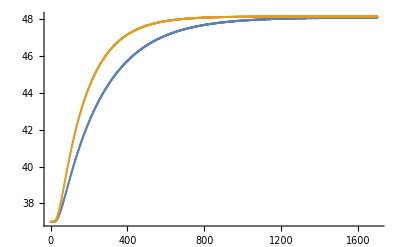

```mathematica
ListPlot[{actual,mesh[[108]]},PlotRange->All]
```

```mathematica
Export["D:\\Mod\\problem1.xlsx",mesh[[108]]];
```

```mathematica
Export["D:\\Mod\\problem1plus.xlsx",mesh];
```

```mathematica
axisConvert[x_]:=Module[
{y},
{
y=If[x<104,(x-1)/10,(x-103)+10.2]
};
y
]
```

```mathematica
Tem3D=Flatten[Table[{axisConvert[i]*10,j-1,mesh[[i]][[j]]},{i,1,109},{j,1,1701}],1];
```

```mathematica
ListPlot3D[Tem3D,ColorFunction->"Rainbow"]
```